```mathematica
ClearAll["Global`*"]
```

```mathematica
Z0=50
```

50

## Functions

```mathematica
SmithTran[z_]:=(z-Z0)/(z+Z0)
```

```mathematica
SmithTranInv[G_]:=-Z0(G+1)/(G-1)
```

```mathematica
ComplexSplit[v_]:=If[Length[v]==0,{Re[v],Im[v]},{Re[#],Im[#]}&/@v]
```

## Plot

```mathematica
v=RandomComplex[{0-50I,50+50I},1000];
```

```mathematica
vSt=SmithTran[v]//N;
```

```mathematica
VStSplit=ComplexSplit[vSt];
```

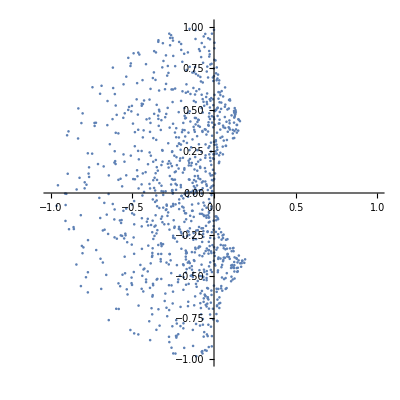

```mathematica
lp=ListPlot[VStSplit,AspectRatio->1,PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
ContourPlot[SmithTran[Z0+I x]==,{x,-100,100},AspectRatio->1,PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
ParametricPlot
```

ParametricPlot

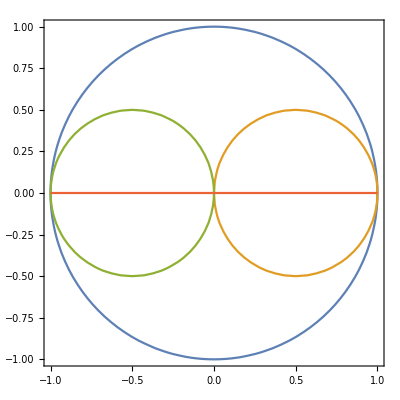

```mathematica
f=ContourPlot[{x^2+y^2==1,(x-0.5)^2+y^2==0.5^2,(x+0.5)^2+y^2==0.5^2,y==0},{x,-1,1},{y,-1,1}]
```

```mathematica
SmithFGrid=Flatten[{-{0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.5,5,10,20},{0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.5,5,10,20}}]
```

{0,-0.25,-0.5,-0.75,-1,-1.25,-1.5,-1.75,-2,-2.5,-5,-10,-20,0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.5,5,10,20}

```mathematica
SmithChartContours={Re[SmithTranInv[x+I y]/Z0]==#&/@SmithFGrid,Im[SmithTranInv[x+I y]/Z0]==#&/@SmithFGrid}//Flatten;
```

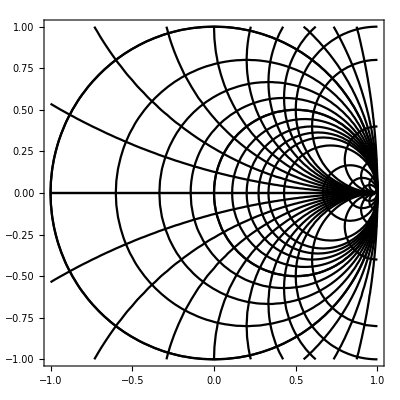

```mathematica
f=ContourPlot[{Re[SmithTranInv[x+I y]/Z0]==1,SmithChartContours//Evaluate},{x,-1,1},{y,-1,1},ContourStyle->Black]
```

```mathematica
Solve[SmithTranInv[x+I y]==1,{x}]
```

{{x→-1/51 ⅈ (-49 ⅈ+51 y)}}

```mathematica
SmithTranInv[x+I y]
```

-(50 (1+x+ⅈ y))/(-1+x+ⅈ y)